```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA_CT",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs}];
```

## t- t (1-loop - self energy)

```mathematica
tops = CreateTopologies[1,1->1,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,WFCorrections}];
topsCT = CreateCTTopologies[1,1->1,ExcludeTopologies->{WFCorrectionCTs,TadpoleCTs,BoxCTs,TriangleCTs}]
processGGT =  { F[9]}-> {F[9]};
allDiags = InsertFields[Join[tops,topsCT],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8],V[4]}];
```

TopologyList(Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(2,1)(3)),Propagator(Outgoing)(Vertex(1)(2),Vertex(2,1)(3))))

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA_CT} initialized

in total: 2 Particles insertions

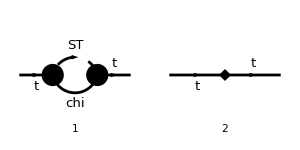

```mathematica
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 300,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{p},LorentzIndexNames->{μ,ν},OutgoingMomenta->{p},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
```

in total: 2 Particles amplitudes

```mathematica
ampC =( TID[ampA,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]);
```

```mathematica
ampC
```

(ⅈ π^2 yDM^2 δ_Col1Col2 (-MT (γ·p).(γ̄)^6 (-((mChi^2-mST^2+p^2) B_0(p^2,mChi^2,mST^2))/(2 p^2)+(A_0(mChi^2))/(2 p^2)-(A_0(mST^2))/(2 p^2))+deltaS (γ·p).(γ̄)^7+deltaSp MT (γ·p).(γ̄)^6+deltaS MT))/MT

## On - shell case

```mathematica
SPD[p,p]=psq;
```

```mathematica
ampD= Simplify[ FeynAmpDenominatorExplicit[ampC]]
```

(ⅈ π^2 yDM^2 δ_Col1Col2 (MT (γ·p).(γ̄)^6 (mChi^2 B_0(psq,mChi^2,mST^2)-mST^2 B_0(psq,mChi^2,mST^2)+psq B_0(psq,mChi^2,mST^2)-A_0(mChi^2)+A_0(mST^2)+2 deltaSp psq)+2 deltaS psq ((γ·p).(γ̄)^7+MT)))/(2 MT psq)

```mathematica
ampE=DiracSimplify[ampD];
```

```mathematica
gammas=Tally[Cases[{ampE},DiracGamma[___].DiracGamma[___],All]][[All,1]]
```

{(γ·p).(γ̄)^6,(γ·p).(γ̄)^7}

```mathematica
ampEsimp=Collect[Expand[ampE],gammas,FullSimplify]
```

(ⅈ π^2 yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6 ((mChi^2-mST^2+psq) B_0(psq,mChi^2,mST^2)-A_0(mChi^2)+A_0(mST^2)+2 deltaSp psq))/(2 psq)+(ⅈ π^2 deltaS yDM^2 δ_Col1Col2 (γ·p).(γ̄)^7)/MT+ⅈ π^2 deltaS yDM^2 δ_Col1Col2

## Renormalization Coefficients

```mathematica
$Assumptions->{mST>0,mChi>0,MT>0,mST>mChi,mST>MT,mST>mChi+MT,ScaleMu>0};
```

```mathematica
fR[psq_]=Collect[Collect[FullSimplify[PaXEvaluate[Coefficient[ampEsimp,gammas[[1]]],PaXImplicitPrefactor->1/(2 Pi)^(4 -2 Epsilon)]/.{ScaleMu-> ScaleMu/(√(4 Pi)),EulerGamma->0}],{Epsilon,Log[a_]},FullSimplify]/.{Log[ScaleMu^2/mChi^2]-> Log[ScaleMu^2/mST^2]-Log[mChi^2/mST^2]},{Epsilon,Log[a_]},FullSimplify];
fL[psq_]=Coefficient[ampEsimp,gammas[[2]]];
(* Include the term without gammas as GA6+GA7 *)
fSR[psq_]=Coefficient[ampEsimp,DiracGamma[6]] + I*deltaS*Pi^2*yDM^2*SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]] ;
fSL[psq_]=Coefficient[ampEsimp,DiracGamma[7]]+ I*deltaS*Pi^2*yDM^2*SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]] ;
```

```mathematica
Print["fL = ",fL[p2]]
Print["fSR = ",fSR[p2]]
Print["fR = ",fR[p2]]
Print["fSL = ",fSL[p2]]
```

fL = (ⅈ deltaS π^2 yDM^2 δ_Col1Col2)/MT

fSR = ⅈ deltaS π^2 yDM^2 δ_Col1Col2

fR = -(ⅈ (mChi^4-2 mST^2 mChi^2+(mST^2-p2)^2) log(mChi^2/mST^2) δ_Col1Col2 yDM^2)/(64 p2^2 π^2)+1/(32 p2^2 π^2)ⅈ (mChi^2-mST^2+p2) √(mChi^4-2 (mST^2+p2) mChi^2+(mST^2-p2)^2) log((mChi^2+mST^2-p2+√(mChi^4-2 (mST^2+p2) mChi^2+(mST^2-p2)^2))/(2 mChi mST)) δ_Col1Col2 yDM^2+(ⅈ log(μ^2/mST^2) δ_Col1Col2 yDM^2)/(32 π^2)+(ⅈ (mChi^2-mST^2+2 (deltaSp+1) p2) δ_Col1Col2 yDM^2)/(32 p2 π^2)+(ⅈ δ_Col1Col2 yDM^2)/(32 ε π^2)

fSL = ⅈ deltaS π^2 yDM^2 δ_Col1Col2

## Renormalization Conditions

```mathematica
solutions=Collect[FullSimplify[Solve[{fL[MT^2] MT + fSR[MT^2]==0,fR[MT^2] MT + fSL[MT^2]==0},{deltaSp,deltaS}]],{Epsilon,Log[a_]}]
```

{{deltaSp→-1/(2 ε)-(mChi^2-mST^2+2 MT^2)/(2 MT^2)+(((mChi^2-mST^2)^2-2 mST^2 MT^2+MT^4) log(mChi^2/mST^2))/(4 MT^4)-(√((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)) (mChi^2-mST^2+MT^2) log((mChi^2+√((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT))+mST^2-MT^2)/(2 mChi mST)))/(2 MT^4)-1/2 log(μ^2/mST^2),deltaS→0}}

```mathematica
cond2=Collect[FullSimplify[(2 MT D[(fL[p2]+fR[p2]) MT + fSL[p2]+fSR[p2],p2]+fL[p2]+fR[p2])/.{p2->MT^2}],{Epsilon,Log[a_]},FullSimplify]
```

(ⅈ yDM^2 δ_Col1Col2 (2 MT (16 π^4 deltaS+deltaSp MT)-3 mChi^2+3 mST^2))/(32 π^2 MT^2)-(ⅈ yDM^2 δ_Col1Col2 (-3 (mChi^2-mST^2)^2+2 mST^2 MT^2+MT^4) log(mChi^2/mST^2))/(64 π^2 MT^4)+(ⅈ yDM^2 δ_Col1Col2 (MT^4 (mST^2-mChi^2)+MT^2 (2 mChi^2 mST^2+3 mChi^4-5 mST^4)-3 (mChi^2-mST^2)^3+MT^6) log((mChi^2+√((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT))+mST^2-MT^2)/(2 mChi mST)))/(32 π^2 MT^4 √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)))+(ⅈ yDM^2 δ_Col1Col2 log(μ^2/mST^2))/(32 π^2)+(ⅈ yDM^2 δ_Col1Col2)/(32 π^2 ε)

```mathematica
Collect[FullSimplify[Solve[(cond2/.{deltaS->0})==0,deltaSp]],{Epsilon,Log[a_]}]
```

{{deltaSp→-1/(2 ε)+((-3 (mChi^2-mST^2)^2+2 mST^2 MT^2+MT^4) log(mChi^2/mST^2))/(4 MT^4)+((MT^2 (-2 mChi^2 mST^2-3 mChi^4+5 mST^4)+3 (mChi^2-mST^2)^3+MT^4 (mChi-mST) (mChi+mST)-MT^6) log((mChi^2+√((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT))+mST^2-MT^2)/(2 mChi mST)))/(2 MT^4 √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)))+(3 (mChi-mST) (mChi+mST))/(2 MT^2)-1/2 log(μ^2/mST^2)}}